5.71386

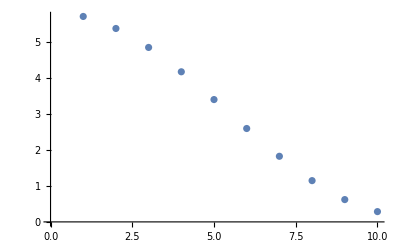

```mathematica
m=10;
A=SparseArray[{
Band[{1,1}]->3.0,
Band[{2,1}]->2.0,
Band[{1,2}]->1.0
},{m,m}];
MatrixForm[A];
evals=Eigenvalues[A];
Max[evals]
ListPlot[evals]
```